## Утилиты

### Работа с файловой системой

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\User\source\repos\Pervansh\STUDY-Boltzmann-1D-solver\Boltzmann_1D_Solver

### Получение данных

#### Получение макропараметров

```mathematica
ReadLastBgk1Results[testDirName_String]:=Module[{path,t,n,u1,T,q1,x},
path="output\\bgk1d\\"<>testDirName;
t=Last@First@Import[path<>"\\t_levels.txt","Table"];
x=Last@Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
n=Last@Import[Evaluate@path<>"\\n.txt","Table"];
u1=Last@Import[Evaluate@path<>"\\u_1.txt","Table"];
T=Last@Import[Evaluate@path<>"\\T.txt","Table"];
q1=Last@Import[Evaluate@path<>"\\q_1.txt","Table"];
Evaluate@<|
"t"->t,
"x"->x,
"n"->n,
"u_1"->u1,
"T"->T,
"q_1"->q1
|>
]
```

```mathematica
ReadFirstBgk1Results[testDirName_String]:=Module[{path,t,n,u1,T,q1,x},
path="output\\bgk1d\\"<>testDirName;
t=First@First@Import[path<>"\\t_levels.txt","Table"];
x=First@Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
n=First@Import[Evaluate@path<>"\\n.txt","Table"];
u1=First@Import[Evaluate@path<>"\\u_1.txt","Table"];
T=First@Import[Evaluate@path<>"\\T.txt","Table"];
q1=First@Import[Evaluate@path<>"\\q_1.txt","Table"];
Evaluate@<|
"t"->t,
"x"->x,
"n"->n,
"u_1"->u1,
"T"->T,
"q_1"->q1
|>
]
```

```mathematica
ReadLastBgk1Results["testSmall"][["x"]]
```

{-0.833333,-0.833333,-0.5,-0.166667,0.166667,0.5,0.833333}

```mathematica
ReadAllBgk1Results[testDirName_String]:=Module[{path,ts,ns,u1s,Ts,q1s,xs},
path="output\\bgk1d\\"<>testDirName;
ts=First@Import[path<>"\\t_levels.txt","Table"];
xs=Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
ns=Import[Evaluate@path<>"\\n.txt","Table"];
u1s=Import[Evaluate@path<>"\\u_1.txt","Table"];
Ts=Import[Evaluate@path<>"\\T.txt","Table"];
q1s=Import[Evaluate@path<>"\\q_1.txt","Table"];
Table[Module[{t,n,u1,T,q1,x},
t=ts[[i]];
x=xs[[i]];
n=ns[[i]];
u1=u1s[[i]];
T=Ts[[i]];
q1=q1s[[i]];
Evaluate@<|
"t"->t,
"x"->x,
"n"->n,
"u_1"->u1,
"T"->T,
"q_1"->q1
|>
],{i,Length@ts}]
]
```

#### Получение функций распределений

```mathematica
ReadLastBgk1Distributions[testDirName_String]:=Module[{path,t,h,g,x,xi},
path="output\\bgk1d\\"<>testDirName;
t=Last@First@Import[path<>"\\t_levels.txt","Table"];
x=Last@Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
xi=Last@Import[Evaluate@path<>"\\xi_1_levels.txt","Table"];
h=Last@SequenceSplit[Import[Evaluate@path<>"\\h.txt","Table"],{{}}];
g=Last@SequenceSplit[Import[Evaluate@path<>"\\g.txt","Table"],{{}}];
Evaluate@<|
"t"->t,
"x"->x,
"xi"->xi,
"h"->h,
"g"->g
|>
]
```

```mathematica
ReadLastBgk1Distributions["testCrash"]
```

<|t→t$12225,x→x$12225,xi→xi$12225,h→h$12225,g→g$12225|>

```mathematica
First@SequenceSplit[{{a,f},{a,d},{},{a},{},{}},{{}}]
```

{{a,f},{a,d}}

```mathematica
ReadAllBgk1Distributions[testDirName_String]:=Module[{path,ts,hs,gs,xs,xis},
path="output\\bgk1d\\"<>testDirName;
ts=First@Import[path<>"\\t_levels.txt","Table"];
xs=Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
xis=Import[Evaluate@path<>"\\xi_1_levels.txt","Table"];
hs=SequenceSplit[Import[Evaluate@path<>"\\h.txt","Table"],{{}}];
gs=SequenceSplit[Import[Evaluate@path<>"\\g.txt","Table"],{{}}];

Table[Module[{t,h,g,x,xi},
t=ts[[i]];
x=xs[[i]];
xi=xis[[i]];
h=hs[[i]];
g=gs[[i]];
Evaluate@<|
"t"->t,
"x"->x,
"xi"->xi,
"h"->h,
"g"->g
|>
],{i,Length@ts}]
]
```

## Построение графиков

### 1D

```mathematica
Macroparameters1dPlot[params_Association]:=Module[{Nx},
Nx=Length@params[["x"]];
Grid[{
{
ListPlot[Table[{params[["x"]][[i]],params[["n"]][[i]]},{i,Nx}],AxesLabel->{"x","n"},PlotRange->Full],
ListPlot[Table[{params[["x"]][[i]],params[["u_1"]][[i]]},{i,Nx}],AxesLabel->{"x","u_1"},PlotRange->Full]
},
{
ListPlot[Table[{params[["x"]][[i]],params[["T"]][[i]]},{i,Nx}],AxesLabel->{"x","T"},PlotRange->Full],
ListPlot[Table[{params[["x"]][[i]],params[["q_1"]][[i]]},{i,Nx}],AxesLabel->{"x","q_1"},PlotRange->Full]
}
}]
]
```

```mathematica
Macroparameters1dPlot[params_Association,rangeAssoc_Association]:=Module[{Nx},
Nx=Length@params[["x"]];
Grid[{
{
ListPlot[Table[{params[["x"]][[i]],params[["n"]][[i]]},{i,Nx}],AxesLabel->{"x","n"},PlotRange->{{rangeAssoc[["x_min"]],rangeAssoc[["x_max"]]},{rangeAssoc[["n_min"]],rangeAssoc[["n_max"]]}}],
ListPlot[Table[{params[["x"]][[i]],params[["u_1"]][[i]]},{i,Nx}],AxesLabel->{"x","u_1"},PlotRange->{{rangeAssoc[["x_min"]],rangeAssoc[["x_max"]]},{rangeAssoc[["u1_min"]],rangeAssoc[["u1_max"]]}}]
},
{
ListPlot[Table[{params[["x"]][[i]],params[["T"]][[i]]},{i,Nx}],AxesLabel->{"x","T"},PlotRange->{{rangeAssoc[["x_min"]],rangeAssoc[["x_max"]]},{rangeAssoc[["T_min"]],rangeAssoc[["T_max"]]}}],
ListPlot[Table[{params[["x"]][[i]],params[["q_1"]][[i]]},{i,Nx}],AxesLabel->{"x","q_1"},PlotRange->{{rangeAssoc[["x_min"]],rangeAssoc[["x_max"]]},{rangeAssoc[["q1_min"]],rangeAssoc[["q1_max"]]}}]
}
}]
]
```

```mathematica
Macroparameters1dRangeAssociation[params_Association]:=Module[{rangeAssoc},
rangeAssoc=<|
"x_min"->+∞,
"x_max"->-∞,
"n_min"->+∞,
"n_max"->-∞,
"u1_min"->+∞,
"u1_max"->-∞,
"T_min"->+∞,
"T_max"->-∞,
"q1_min"->+∞,
"q1_max"->-∞
|>;

rangeAssoc[["x_min"]]=Min[{rangeAssoc[["x_min"]]},params[["x"]]];
rangeAssoc[["x_max"]]=Max[{rangeAssoc[["x_max"]]},params[["x"]]];
rangeAssoc[["n_min"]]=Min[{rangeAssoc[["n_min"]]},params[["n"]]];
rangeAssoc[["n_max"]]=Max[{rangeAssoc[["n_max"]]},params[["n"]]];
rangeAssoc[["u1_min"]]=Min[{rangeAssoc[["u1_min"]]},params[["u_1"]]];
rangeAssoc[["u1_max"]]=Max[{rangeAssoc[["u1_max"]]},params[["u_1"]]];
rangeAssoc[["T_min"]]=Min[{rangeAssoc[["T_min"]]},params[["T"]]];
rangeAssoc[["T_max"]]=Max[{rangeAssoc[["T_max"]]},params[["T"]]];
rangeAssoc[["q1_min"]]=Min[{rangeAssoc[["q1_min"]]},params[["q_1"]]];
rangeAssoc[["q1_max"]]=Max[{rangeAssoc[["q1_max"]]},params[["q_1"]]];

rangeAssoc
];

rangeAssocKeys=<|
"x"-><|"min"->"x_min","max"->"x_max"|>,
"n"-><|"min"->"n_min","max"->"n_max"|>,
"u_1"-><|"min"->"u1_min","max"->"u1_max"|>,
"T"-><|"min"->"T_min","max"->"T_max"|>,
"q_1"-><|"min"->"q1_min","max"->"q1_max"|>
|>;
```

```mathematica
Macroparameters1dRangeAssociation[params_List]:=Module[{rangeAssoc},
rangeAssoc=<|
"x_min"->+∞,
"x_max"->-∞,
"n_min"->+∞,
"n_max"->-∞,
"u1_min"->+∞,
"u1_max"->-∞,
"T_min"->+∞,
"T_max"->-∞,
"q1_min"->+∞,
"q1_max"->-∞
|>;

Do[
rangeAssoc[["x_min"]]=Min[{rangeAssoc[["x_min"]]},subParams[["x"]]];
rangeAssoc[["x_max"]]=Max[{rangeAssoc[["x_max"]]},subParams[["x"]]];
rangeAssoc[["n_min"]]=Min[{rangeAssoc[["n_min"]]},subParams[["n"]]];
rangeAssoc[["n_max"]]=Max[{rangeAssoc[["n_max"]]},subParams[["n"]]];
rangeAssoc[["u1_min"]]=Min[{rangeAssoc[["u1_min"]]},subParams[["u_1"]]];
rangeAssoc[["u1_max"]]=Max[{rangeAssoc[["u1_max"]]},subParams[["u_1"]]];
rangeAssoc[["T_min"]]=Min[{rangeAssoc[["T_min"]]},subParams[["T"]]];
rangeAssoc[["T_max"]]=Max[{rangeAssoc[["T_max"]]},subParams[["T"]]];
rangeAssoc[["q1_min"]]=Min[{rangeAssoc[["q1_min"]]},subParams[["q_1"]]];
rangeAssoc[["q1_max"]]=Max[{rangeAssoc[["q1_max"]]},subParams[["q_1"]]];
,{subParams,params}];

rangeAssoc
];
```

```mathematica
rangeAssocKeys=<|
"x"-><|"min"->"x_min","max"->"x_max"|>,
"n"-><|"min"->"n_min","max"->"n_max"|>,
"u_1"-><|"min"->"u1_min","max"->"u1_max"|>,
"T"-><|"min"->"T_min","max"->"T_max"|>,
"q_1"-><|"min"->"q1_min","max"->"q1_max"|>
|>;
```

```mathematica
Macroparameter1dPlot[params_Association,paramName_String]:=Module[{Nx},
Nx=Length@params[["x"]];
ListPlot[Table[{params[["x"]][[i]],params[[paramName]][[i]]},{i,Nx}],AxesLabel->{"x",paramName},PlotRange->Full]
]
```

```mathematica
Macroparameter1dPlot[params_Association,rangeAssoc_Association,paramName_String,opts_List:{}]:=Module[{Nx},
Nx=Length@params[["x"]];
ListPlot[Table[{params[["x"]][[i]],params[[paramName]][[i]]},{i,Nx}],AxesLabel->{"x",paramName},PlotRange->{{rangeAssoc[["x_min"]],rangeAssoc[["x_max"]]},{rangeAssoc[[rangeAssocKeys[[paramName,"min"]]]],rangeAssoc[[rangeAssocKeys[[paramName,"max"]]]]}},Sequence@@opts]
]
```

```mathematica
Macroparameter1dLinePlot[params_Association,rangeAssoc_Association,paramName_String,opts_List:{}]:=Module[{Nx},
Nx=Length@params[["x"]];
ListLinePlot[Table[{params[["x"]][[i]],params[[paramName]][[i]]},{i,Nx}],AxesLabel->{"x",paramName},PlotRange->{{rangeAssoc[["x_min"]],rangeAssoc[["x_max"]]},{rangeAssoc[[rangeAssocKeys[[paramName,"min"]]]],rangeAssoc[[rangeAssocKeys[[paramName,"max"]]]]}},Sequence@@opts]
]
```

```mathematica
Distribution1dPrint[params_Association]:=Module[{Nx,Nxi},
Nx=Length@params[["x"]];
Nxi=Length@params[["xi"]];
Grid[{
{
ListPointPlot3D[Table[{params[["x"]][[i]],params[["xi"]][[j]],params[["h"]][[i,j]]},{i,Nx},{j,Nxi}],AxesLabel->{"x","xi","h"}],
Manipulate[Grid[Transpose@{{
params[["x"]][[i]],
ListPlot[Table[{params[["xi"]][[j]],params[["h"]][[i,j]]},{j,Length@params[["xi"]]}],AxesLabel->{"xi","h"},PlotRange->Full]
}}],{i,1,Length@params[["x"]],1}],
Manipulate[Grid[Transpose@{{
params[["xi"]][[j]],
ListPlot[Table[{params[["x"]][[i]],params[["h"]][[i,j]]},{i,Length@params[["x"]]}],AxesLabel->{"x","h"},PlotRange->Full]
}}],{j,1,Length@params[["xi"]],1}]
}
,
{
ListPointPlot3D[Table[{params[["x"]][[i]],params[["xi"]][[j]],params[["g"]][[i,j]]},{i,Nx},{j,Nxi}],AxesLabel->{"x","xi","g"}],
Manipulate[Grid[Transpose@{{
params[["x"]][[i]],
ListPlot[Table[{params[["xi"]][[j]],params[["g"]][[i,j]]},{j,Length@params[["xi"]]}],AxesLabel->{"xi","g"},PlotRange->Full]
}}],{i,1,Length@params[["x"]],1}],
Manipulate[Grid[Transpose@{{
params[["xi"]][[j]],
ListPlot[Table[{params[["x"]][[i]],params[["g"]][[i,j]]},{i,Length@params[["x"]]}],AxesLabel->{"x","g"},PlotRange->Full]
}}],{j,1,Length@params[["xi"]],1}]
}
}]
]
```

## БГК 1

### Распад разрыва для плотности

#### Последний временной слой

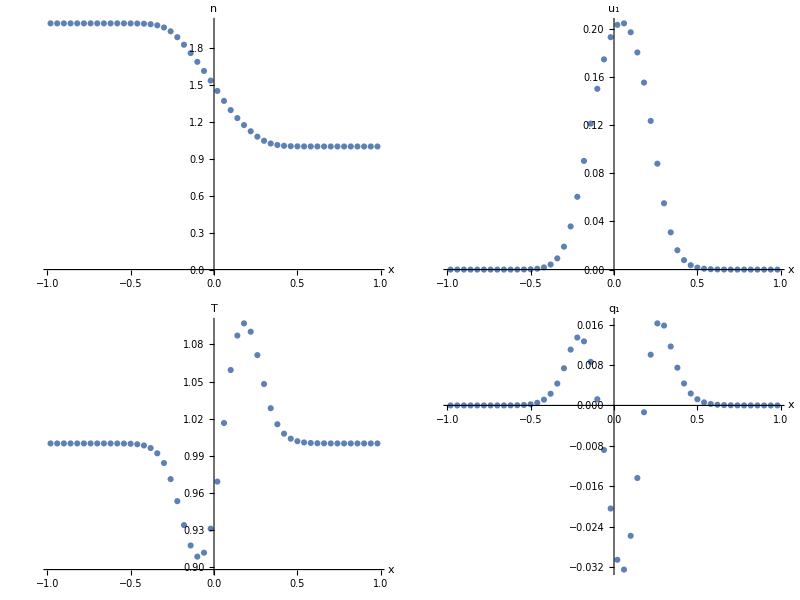

-Graphics3D- |  | 
-Graphics3D- |  |

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

```mathematica
Module[{params},
params=ReadLastBgk1Results["testDensity"];
Macroparameters1dPlot[params]
]
Module[{params},
params=ReadLastBgk1Distributions["testDensity"];
Distribution1dPrint[params]
]
```

#### Временной промежуток перед концом

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testDensityMultiple"];
Export["testDensityMultiple.mp4",Table[Macroparameters1dPlot[params[[i]]],{i,1,40,1}]];

Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

### Распад разрыва для плотности, отношение 10/1

#### Взятие примера данных

```mathematica
ReadExternalEulerResults[fileName_String]:=Module[{path,data,x,n,u1,T,q1},
path=fileName<>".txt";
data=Transpose@Rest@Import[Evaluate@path,"Table"];
x=Evaluate@data[[1]];
n=Evaluate@data[[2]];
u1=Evaluate@data[[3]];
Evaluate@<|
"x"->Evaluate@x,
"n"->Evaluate@n,
"u_1"->Evaluate@u1
|>
]
```

#### Последний временной слой

```mathematica
Module[{params},
params=ReadLastBgk1Results["testDensity"];
Macroparameters1dPlot[params]
]
Module[{params},
params=ReadLastBgk1Distributions["testDensity"];
Distribution1dPrint[params]
]
```

-Graphics-

-Graphics3D- |  | 
-Graphics3D- |  |

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

#### Временной промежуток перед концом

```mathematica
DynamicModule[{params,rangeAssoc},
params=ReadAllBgk1Results["testDensity10Multiple"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
Export["testDensity10Multiple.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]];

Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]
]

(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

```mathematica
DynamicModule[{params,rangeAssoc,extParams,res},
params=ReadAllBgk1Results["testDensity10Multiple"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
rangeAssoc[["n_min"]]=0.;
extParams=ReadExternalEulerResults["extra\\TitarevDensityResultsCorrect"];
Manipulate[ Show[Macroparameter1dPlot[params[[i]],rangeAssoc,"n"],Macroparameter1dLinePlot[extParams,rangeAssoc,"n",{PlotStyle->{Black,Thickness[0.002]}}]],{i,1,Length@params,1}]
(*Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1.5+0.5Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]*)
]
```

```mathematica
DynamicModule[{params,rangeAssoc,extParams,res},
params=ReadAllBgk1Results["SOD_1"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
rangeAssoc[["n_min"]]=0.;
extParams=ReadExternalEulerResults["extra\\TitarevDensityResultsCorrect"];
Manipulate[ Show[Macroparameter1dPlot[params[[i]],rangeAssoc,"n"],Macroparameter1dLinePlot[extParams,rangeAssoc,"n",{PlotStyle->{Black,Thickness[0.002]}}]],{i,1,Length@params,1}]
(*Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1.5+0.5Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]*)
]
```

```mathematica
DynamicModule[{params,rangeAssoc},
params=ReadAllBgk1Results["SOD_1"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
(*Export["testDensity10Multiple.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]]*);

Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]
]

(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

#### Сравнение на последнем временном слое

```mathematica
DynamicModule[{params,rangeAssoc,extParams,res},
params=ReadLastBgk1Results["testDensity10Multiple"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
rangeAssoc[["n_min"]]=0.;
extParams=ReadExternalEulerResults["extra\\TitarevDensityResultsCorrect"];
res=Show[Macroparameter1dPlot[params,rangeAssoc,"n"],Macroparameter1dLinePlot[extParams,rangeAssoc,"n",{PlotStyle->{Black,Thickness[0.002]}}]];
Export["postprocessing\\desnityRiemannProblemComparison.pdf",res];
Export["postprocessing\\desnityRiemannProblemComparison.jpg",res];
res
(*Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1.5+0.5Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]*)
]
DynamicModule[{params,rangeAssoc},
params=ReadLastBgk1Results["testDensity10Multiple"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
rangeAssoc[["n_min"]]=0.;
Macroparameters1dPlot[params,rangeAssoc]
(*Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1.5+0.5Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]*)
]
```

```mathematica
DynamicModule[{params,rangeAssoc,extParams,res},
params=ReadLastBgk1Results["SOD_1"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
rangeAssoc[["n_min"]]=0.;
extParams=ReadExternalEulerResults["extra\\TitarevDensityResultsCorrect"];
res=Show[Macroparameter1dPlot[params,rangeAssoc,"n"],Macroparameter1dLinePlot[extParams,rangeAssoc,"n",{PlotStyle->{Black,Thickness[0.002]}}]];
Export["postprocessing\\SOD_1.pdf",res];
Export["postprocessing\\SOD_1.jpg",res];
res
(*Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1.5+0.5Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]*)
]
DynamicModule[{params,rangeAssoc},
params=ReadLastBgk1Results["testDensity10Multiple"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
rangeAssoc[["n_min"]]=0.;
Macroparameters1dPlot[params,rangeAssoc]
(*Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1.5+0.5Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]*)
]
```

### Распад разрыва для плотности при свободно молекулярном течении

#### Последний временной слой

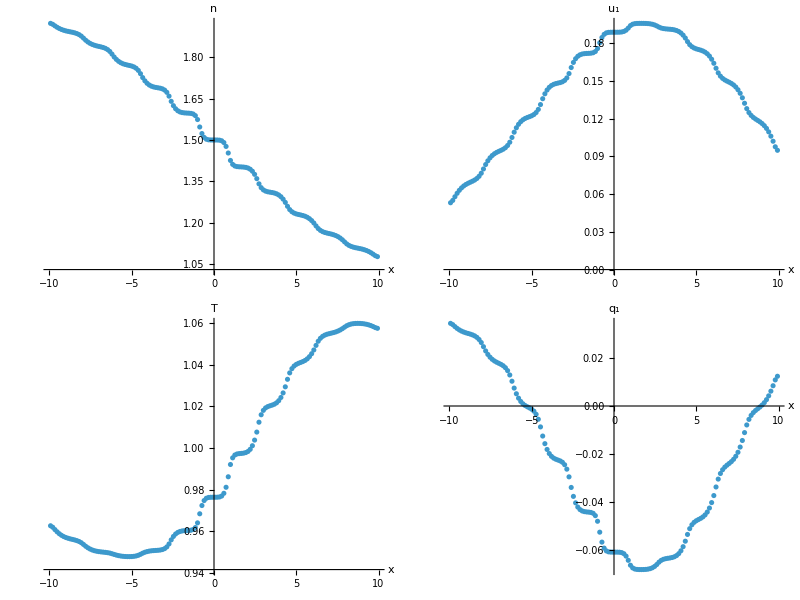

-Graphics3D- |  | 
-Graphics3D- |  |

```mathematica
Module[{params},
params=ReadLastBgk1Results["testFreeMoleculeDensity"];
Macroparameters1dPlot[params]
]
Module[{params},
params=ReadLastBgk1Distributions["testFreeMoleculeDensity"];
Distribution1dPrint[params]
]
```

#### Макропараметры на всем временном промежутке

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testFreeMoleculeDensity"];
Export["testFreeMoleculeDensity.mp4",Table[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]];

Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

#### Макропараметры на всем временном промежутке в случае сдвига

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testFreeMoleculeDensityShifted"];
Export["testFreeMoleculeDensityShifted.mp4",Table[Macroparameters1dPlot[params[[i]]],{i,1,40,1}]];

Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testFreeMoleculeDensityShifted"];
Export["testFreeMoleculeDensityShiftedExpected.mp4",Table[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1+Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]];

Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1.5+0.5Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5},PlotStyle->{Black,Thin}]],{i,2,Length@params-1,1}]
]
```

Show::gcomb: Could not combine the graphics objects in 
    Show[Macroparameter1dPlot[<|t -> t$209335, x -> x$209335, n -> n$209335, 
       u  -> u1$209335, T -> T$209335, q  -> q1$209335|>, n], -Graphics-].
        1                               1

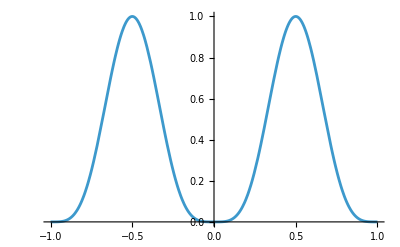
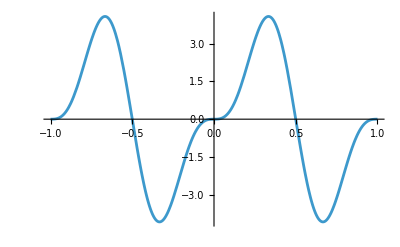
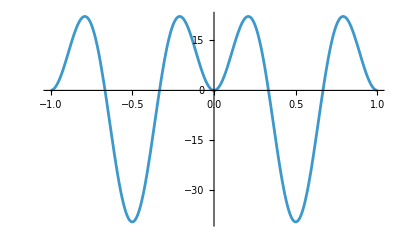
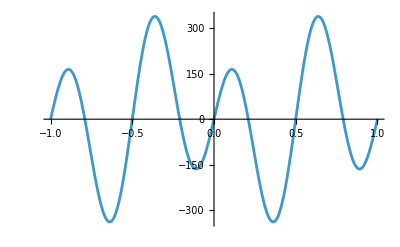
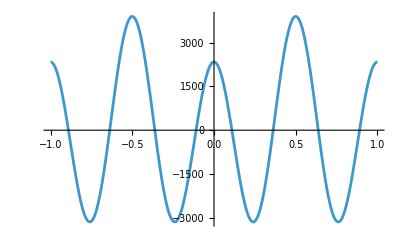

```mathematica
Table[Plot[D[(Sin[π y])^4,{y,k}]/.y->x, {x,-1,1}],{k,0,4}]
```

### Испускающая стенка

#### Молекулы-шары

```mathematica
DynamicModule[{params,rangeAssoc},
params=ReadAllBgk1Results["testEmittingWallBall"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
Export["postprocessing\\testEmittingWallBall.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]];

Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

#### Максвелловские молекулы

```mathematica
DynamicModule[{params,rangeAssoc},
params=ReadAllBgk1Results["testEmittingWallMaxwell"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
Export["postprocessing\\testEmittingWallMaxwell.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]];

Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

### Испаряющаяся стенка

#### Максвелловские молекулы

```mathematica
DynamicModule[{params,rangeAssoc,res},
params=ReadAllBgk1Results["testEvaporatingWallMaxwell"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
(*rangeAssoc[["n_max"]]=40;*)
(*Export["postprocessing\\testEvaporatingWallMaxwell.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]]*);
res=Show[Sequence@@Table[Macroparameter1dLinePlot[params[[i]],rangeAssoc,"n"],{i,1,Length@params,1}]];
Export["postprocessing\\evaporatingProblem\\figure_3_test.jpeg",res];
res
(*Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]*)
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

```mathematica
DynamicModule[{params,rangeAssoc,res},
params=ReadAllBgk1Results["testEvaporatingWallMaxwell2"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
(*rangeAssoc[["n_max"]]=40;*)
(*Export["postprocessing\\testEvaporatingWallMaxwell.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]]*);
res=Show[Sequence@@Table[Macroparameter1dLinePlot[params[[i]],rangeAssoc,"n"],{i,1,Length@params,1}]];
Export["postprocessing\\evaporatingProblem\\figure_3_test2.jpeg",res];
Grid@{{res},{Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]}}
(*Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]*)
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

```mathematica
DynamicModule[{params,rangeAssoc,res},
params=ReadAllBgk1Results["testEvaporatingWallMaxwell3"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
(*rangeAssoc[["n_max"]]=40;*)
(*Export["postprocessing\\testEvaporatingWallMaxwell.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]]*);
res=Show[Sequence@@Table[Macroparameter1dLinePlot[params[[i]],rangeAssoc,"n"],{i,1,Length@params,1}]];
Export["postprocessing\\evaporatingProblem\\figure_3_test3.jpeg",res];
Grid@{{res},{Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]}}
(*Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]*)
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

```mathematica
DynamicModule[{params,rangeAssoc,res},
params=ReadAllBgk1Results["testEvaporatingWallMaxwell4"];
rangeAssoc=Macroparameters1dRangeAssociation[params];
(*rangeAssoc[["n_max"]]=40;*)
(*Export["postprocessing\\testEvaporatingWallMaxwell.mp4",Table[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]]*);
res=Show[Sequence@@Table[Macroparameter1dLinePlot[params[[i]],rangeAssoc,"n"],{i,1,Length@params,1}]];
Export["postprocessing\\evaporatingProblem\\figure_3_test4.jpeg",res];
Grid@{{res},{Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]}}
(*Manipulate[Macroparameters1dPlot[params[[i]],rangeAssoc],{i,1,Length@params,1}]*)
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

## Всякие расчеты

### Правило трех сигм

```mathematica
Erf[3]//N
```

0.999978

```mathematica
Erf[+∞]
```

1